```mathematica
ks = {0.005,0.01,0.05,0.1};
legend = Table["k="<>ToString[l], {l, ks}]
```

{k=0.005,k=0.01,k=0.05,k=0.1}

```mathematica
FP = -D[p[x,t], t]+k*D[x*p[x, t], x]+(k/2)*D[p[x, t], {x,2}]
```

-p^(0,1)[x,t]+k (p[x,t]+x p^(1,0)[x,t])+1/2 k p^(2,0)[x,t]

```mathematica
p0 = Table[N[PDF[NormalDistribution[5, 1/Sqrt[2]], x]],{k,ks}]
```

{0.56419 2.71828^(-1. (-5.+x)^2),0.56419 2.71828^(-1. (-5.+x)^2),0.56419 2.71828^(-1. (-5.+x)^2),0.56419 2.71828^(-1. (-5.+x)^2)}

```mathematica
bc =p[1, t]==0
```

p[1,t]==0

```mathematica
NDSolverParams[param_, ic_] :=Module[{N},
N = NDSolve[{(FP/.k->param)==0,
 p[x, 0]==ic, 
p[1, t]==0, 
p[20,t]==0},
 p, {x, 1, 20}, {t, 0, 600}, 
MaxStepSize->0.1, 
Method->"MethodOfLines"];
Return[(p/.N[[1]])];
]
```

```mathematica
sols=MapThread[NDSolverParams, {ks, p0}];
```

```mathematica
Manipulate[Plot[sols[[1]][x,t], {x, 1, 20}, PlotRange->{-0.01, 1}], {t, 0, 600}]
```

```mathematica
S[P_] := Integrate[P, {x, 1,20}] 
F[S_]:=D[-S, t]
```

```mathematica
Ss = Table[S[p[x,t]],{p, sols}]
Fs = Table[F[s], {s, Ss}]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

{-InterpolatingFunction[…][t],-InterpolatingFunction[…][t],-InterpolatingFunction[…][t],-InterpolatingFunction[…][t]}

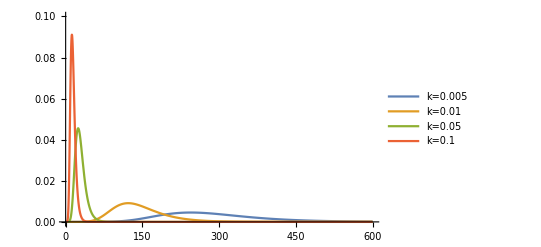

```mathematica
Plot[Fs, {t, 0, 600}, PlotRange->{0,0.1}, PlotLegends->legend]
```

```mathematica
NIntegrate[Fs[[2]], {t, 0, 600}]
```

0.999994